```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&_∈Reals;
x1[theta_,z_]={rh*Cos[theta],rh*Sin[theta],z};
x0={rh,0,0};
dx[theta_,z_]=x1[theta,z]-x0;
rApx[theta_,z_]=dx[theta,z][[3]];
(*leading order*)StokesletsApx[theta_,z_]={{1/rApx[theta,z],0,0},{0,1/rApx[theta,z],0},{0,0,2/rApx[theta,z]}};
MatrixForm[StokesletsApx[theta,z]];
RotF[theta_]={{Cos[theta],-Sin[theta],0},{Sin[theta],Cos[theta],0},{0,0,1}};
MatrixForm[RotF[theta]];
SrotApx[z_]=Simplify[Integrate[StokesletsApx[theta,z].RotF[theta],{theta,0,2*Pi}]];
MatrixForm[SrotApx[z]];
MrotApx[z_]=2*Integrate[SrotApx[z],z];(*×2 becouse integrate over both sides.*)
MatrixForm[MrotApx[z]];
Mrot[z_]={{d11,0,0},{0,d22,0},{0,0,d33+MrotApx[z][[3,3]]}};
MatrixForm[Mrot[z]]
InvMrot[z_]=FullSimplify[Inverse[Mrot[z]]];
MatrixForm[InvMrot[z]]
```

(d11 | 0 | 0
0 | d22 | 0
0 | 0 | d33+8 π Log[z])

(1/d11 | 0 | 0
0 | 1/d22 | 0
0 | 0 | 1/(d33+8 π Log[z]))

Inf cylinder inside inf cylinder, calculate force density.

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&_∈Reals;
zrh=rh/R;
f[rh_,R_]=FullSimplify[2*Pi*((1+4*Log[zrh])*zrh^4-(1-2*zrh^2)^2)/
((1-zrh^2) ((1-zrh^2)+(1+zrh^2)*Log[zrh]))];
f[rh,R]
FullSimplify[-(2 π (R^4))/((R^2)^2+(R^4) Log[rh/R])]
```

-(2 π (R^4-4 R^2 rh^2+3 rh^4+4 rh^4 Log[R/rh]))/((R^2-rh^2)^2+(R^4-rh^4) Log[rh/R])

-(2 π)/(1-Log[R]+Log[rh])

```mathematica
f[1,k*lh]
```

```mathematica
FullSimplify[-(2 π (k^4 lh^4))/((k^2 lh^2)^2+(k^4 lh^4) Log[1/(k lh)])]
```

-(2 π)/(1+Log[1/(k lh)])

```mathematica
Expand[Numerator[f[rh,R]/(2*Pi)]]
Expand[Denominator[f[rh,R]]]
```

-R^4+4 R^2 rh^2-3 rh^4-4 rh^4 Log[R/rh]

R^4-2 R^2 rh^2+rh^4+R^4 Log[rh/R]-rh^4 Log[rh/R]

-q1

-(2 π (R^4-4 R^2 rh^2+(3+4 q1) rh^4))/((R^2-rh^2)^2+R^4 Log[rh/R])

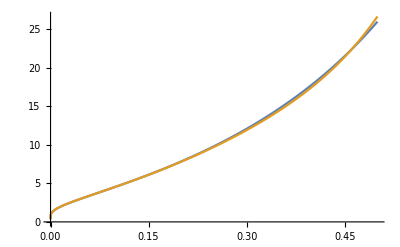

(-2*Pi*(R**4 - 4*R**2*rh**2 + (3 + 4*q1)*rh**4))/((R**2 - rh**2)**2 + R**4*Log(rh/R))

```mathematica
logApx=Normal[Series[Log[x],{x,Exp[-q1],0}]]
fapx[rh_,R_,q1_]=FullSimplify[(2 π (-R^4+4 R^2 rh^2-3 rh^4+4 rh^4 *logApx))/(R^4-2 R^2 rh^2+rh^4+R^4 Log[rh/R])];
fapx[rh,R,q1]
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
t1=fapx[rh,R,q1];
FortranForm[t1]
SetOptions[$Output,PageWidth->pw];
(*Plot[{f[rh,1],fapx[rh,1,1.464868309020669556730354088358581066131591796875]},{rh,0,0.5}]*)
Plot[{f[rh,1],fapx[rh,1,1.464868309020669556730354088358581066131591796875]},{rh,0,0.5}]
```

```mathematica
FullSimplify[fapx[rh,R,q1]]
FullSimplify[fapx[1,1/rh,q1]*rh]
FullSimplify[fapx[rh,1,q1]]
```

-(2 π (R^4-4 R^2 rh^2+(3+4 q1) rh^4))/((R^2-rh^2)^2+R^4 Log[rh/R])

-(2 π rh (1-4 rh^2+(3+4 q1) rh^4))/((-1+rh^2)^2+Log[rh])

-(2 π (1-4 rh^2+(3+4 q1) rh^4))/((-1+rh^2)^2+Log[rh])

```mathematica
Series[-(2 π (1-4 rh^2))/((-1+rh^2)^2+Log[rh]),{rh,0, 3}]
```

-(2 π)/(1+Log[rh])+(4 π (1+2 Log[rh]) rh^2)/(1+Log[rh])^2+O[rh]^4

```mathematica
FullSimplify[-(2 π (1-4 rh^2))/(1-2*rh^2+Log[rh])/.rh-> (rh/(kl*lh))]
```

-(2 π (1-(4 rh^2)/(kl^2 lh^2)))/(1-(2 rh^2)/(kl^2 lh^2)+Log[rh/(kl lh)])